Noanah Malati

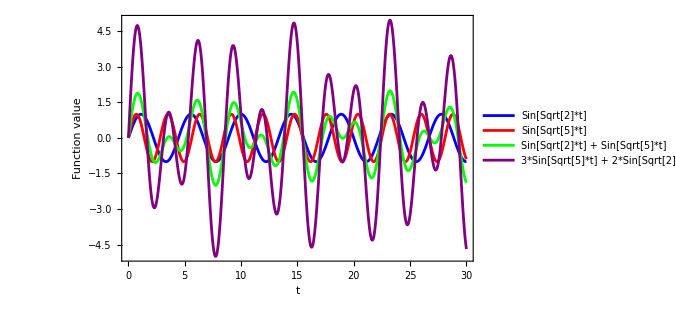

```mathematica
(* Define the functions *)
f1[t_] := Sin[Sqrt[2] * t]
f2[t_] := Sin[Sqrt[5] * t]
f3[t_] := Sin[Sqrt[2] * t] + Sin[Sqrt[5] * t]
f4[t_] := 3 * Sin[Sqrt[5] * t] + 2 * Sin[Sqrt[2] * t]

(* Plot each function *)
Plot[{f1[t], f2[t], f3[t], f4[t]}, {t, 0, 30}, 
    PlotLegends -> {"Sin[Sqrt[2]*t]", "Sin[Sqrt[5]*t]", "Sin[Sqrt[2]*t] + Sin[Sqrt[5]*t]", 
    "3*Sin[Sqrt[5]*t] + 2*Sin[Sqrt[2]*t]"}, 
    PlotStyle -> {Blue, Red, Green, Purple}, 
    Frame -> True, 
    FrameLabel -> {"t", "Function value"}, 
    PlotRange -> All, 
    ImageSize -> 500]
```